# QFT compilation with training states

```mathematica
MatrixDist::usage="MatrixDist[matrix1, matrix2, plotglobalphase:False]. Calculate distance of 2 matrices by max_λ |(U-V)|, 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,plotglobalphase_:False]:=Module[{globalphase,mindist,F,ϕ},
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"}]];
{mindist,ϕ/.globalphase}
]

QFT::usage="Return Quantum Fourier Transform for nqubits. For a functioning circuit -- not only aesthetically pleasing,
 one must flatten it: QFT[nqubit]//Flatten ";QFT[nqubit_,swap_:True]:=Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]

SetAttributes[CompileMe,HoldAll]
CompileMe[nq_,matrix_,conf_,printmatrices_:False]:=Module[{dist,globalphase},
{runtime,{costlist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim,corrmat}}=AbsoluteTiming[Recompile[nq,conf]];
Print[{ansatz,θvars,aborted,fev,ncycle,"{merged, θsmall, metric, bruteforce}=",elim,finmsg,corrmat}];
(*
Print[ListPlot[costlist,PlotRange->All,Joined->True,PlotMarkers->{Automatic,None}]];
*)
Print[DrawCircuit[ansatz,nq]];
Print["cost=",Last@costlist,"; ngates=",Length@ansatz];
Print["runtime= ",runtime/60," minutes"];

vmat=ConjugateTranspose@CalcCircuitMatrix[ansatz/.CustomGatesDefinitions/.θvars,nq];
{dist,globalphase}=MatrixDist[matrix,vmat];
Print["cost=",Last@costlist, " ;dist=",dist, "; globalphase=",globalphase];
Print["final correlation matrix :",MatrixForm@corrmat];
If[printmatrices,
Print[MatrixForm@Chop[Exp[ⅈ*globalphase]*vmat]];
]
]
```

## No-swap QFT

Note: not enough training data makes it difficult to find gradient

#### 3 - QFT

```mathematica
unitary3=CalcCircuitMatrix@Flatten@QFT[3,False];
conf=DefaultConfig[3,unitary3,6];
```

@cycle1:Wed 6 Jul 2022 21:32:04, fev:73, <E>: 0.21537365293798605 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 0, 0}

@cycle2:Wed 6 Jul 2022 21:32:19, fev:220, <E>: 0.11111147856711477 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 15, 2, 0, 3}

{{Rz_0[θ_4],Rx_2[θ_10],C_1[Rx_2[θ_26]],Rz_1[θ_12],C_0[Rx_2[θ_13]],C_0[Ry_1[θ_27]],Ry_2[θ_14],Ry_1[θ_19],Ry_0[θ_28],Rx_1[θ_20],C_1[Rz_2[θ_29]]},<|θ_4→1.57107,θ_10→3.14168,θ_12→1.178,θ_13→-1.5701,θ_14→-1.57093,θ_19→1.57113,θ_20→1.57093,θ_26→-0.786085,θ_27→-1.5707,θ_28→1.57228,θ_29→-0.0000720386|>,{},259,3,{merged, θsmall, metric, bruteforce}=,{0,15,2,0},Circuit within target precision is found,{{3.33877×10^-8,4.77995×10^-8,5.23652×10^-8},{4.77995×10^-8,1.44118×10^-8,3.33892×10^-8},{5.23652×10^-8,3.33892×10^-8,1.89774×10^-8}}}

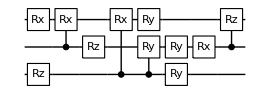

cost=2.45751×10^-7; ngates=11

runtime= 0.419201 minutes

cost=2.45751×10^-7 ;dist=0.00108754; globalphase=2.55256

final correlation matrix :(3.33877×10^-8 | 4.77995×10^-8 | 5.23652×10^-8
4.77995×10^-8 | 1.44118×10^-8 | 3.33892×10^-8
5.23652×10^-8 | 3.33892×10^-8 | 1.89774×10^-8)

```mathematica
CompileMe[3,unitary3,conf]
```

#### 5 - QFT

```mathematica
unitary5=CalcCircuitMatrix@Flatten@QFT[5,False];
```

```mathematica
DestroyAllQuregs[]
conf5=DefaultConfig[5,unitary5,15];
```

@cycle1:Thu 7 Jul 2022 00:03:20, fev:213, <E>: 0.3237791239098981 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 18, 1, 0, 3}

@cycle2:Thu 7 Jul 2022 00:04:55, fev:450, <E>: 0.1077552825864005 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 43, 3, 0, 10}

@cycle3:Thu 7 Jul 2022 00:06:04, fev:592, <E>: 0.05160062902014293 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 61, 5, 1, 13}

@cycle4:Thu 7 Jul 2022 00:08:15, fev:804, <E>: 0.011438330596789992 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 79, 7, 1, 18}

@cycle5:Thu 7 Jul 2022 00:10:31, fev:1016, <E>: 0.0029820565840811683 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 100, 9, 1, 21}

@cycle6:Thu 7 Jul 2022 00:13:03, fev:1237, <E>: 0.0025272933792358436 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 117, 11, 1, 26}

@cycle7:Thu 7 Jul 2022 00:15:39, fev:1471, <E>: 0.0006069233635983014 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 132, 15, 1, 31}

@cycle8:Thu 7 Jul 2022 00:18:32, fev:1696, <E>: 0.0005171474839537967 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 146, 17, 2, 35}

@cycle9:Thu 7 Jul 2022 00:21:51, fev:2001, <E>: 6.754333558382323e-7 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 169, 21, 2, 37}

{{C_2[Rx_4[θ_221]],C_3[Rz_1[θ_170]],Rx_2[θ_163],C_1[Rz_3[θ_171]],Ry_2[θ_168],C_1[Rx_4[θ_127]],Rx_2[θ_175],Rz_1[θ_40],C_3[Rx_4[θ_135]],C_0[Rx_3[θ_41]],Ry_3[θ_2],C_0[Rx_4[θ_58]],C_3[Rx_2[θ_64]],Ry_4[θ_59],Rz_3[θ_14],C_2[Rz_1[θ_89]],Rz_4[θ_4],C_3[Rz_1[θ_77]],C_0[Rz_2[θ_6]],C_0[Rx_1[θ_19]],Rx_2[θ_75],Ry_0[θ_30],Ry_1[θ_20],Rz_2[θ_114]},<|θ_2→-1.57081,θ_4→3.14154,θ_6→1.57198,θ_14→2.5519,θ_19→1.5702,θ_20→1.57089,θ_30→1.57076,θ_40→1.86535,θ_41→-1.57103,θ_58→-1.57101,θ_59→-1.57025,θ_64→-0.392876,θ_75→3.1415,θ_77→-0.785555,θ_89→0.785216,θ_114→-0.390798,θ_127→-0.785397,θ_135→-0.196052,θ_163→-0.000276357,θ_168→1.57068,θ_170→0.195971,θ_171→-0.196415,θ_175→-0.195726,θ_221→-0.39275|>,{},2272,9,{merged, θsmall, metric, bruteforce}=,{0,170,21,2},Circuit within target precision is found,{{0.000304436,0.000817594,0.00106161,0.000480645,0.000943917},{0.000817594,0.000513159,0.00127034,0.000689368,0.00115264},{0.00106161,0.00127034,0.000757179,0.000933388,0.00139666},{0.000480645,0.000689368,0.000933388,0.000176209,0.000815691},{0.000943917,0.00115264,0.00139666,0.000815691,0.000639482}}}

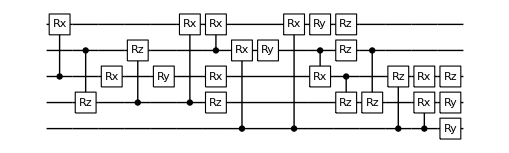

cost=2.41102×10^-7; ngates=24

runtime= 21.2081 minutes

cost=2.41102×10^-7 ;dist=0.00163671; globalphase=0.834414

final correlation matrix :(0.000304436 | 0.000817594 | 0.00106161 | 0.000480645 | 0.000943917
0.000817594 | 0.000513159 | 0.00127034 | 0.000689368 | 0.00115264
0.00106161 | 0.00127034 | 0.000757179 | 0.000933388 | 0.00139666
0.000480645 | 0.000689368 | 0.000933388 | 0.000176209 | 0.000815691
0.000943917 | 0.00115264 | 0.00139666 | 0.000815691 | 0.000639482)

```mathematica
CompileMe[5,unitary5,conf5]
```

#### 8 - QFT

```mathematica
unitary8=CalcCircuitMatrix@Flatten@QFT[8,False];
conf8=DefaultConfig[8,unitary8,20];
```

@cycle1:Thu 7 Jul 2022 00:29:49, fev:197, <E>: 0.49933162686453264 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 1, 7}

@cycle2:Thu 7 Jul 2022 00:33:37, fev:427, <E>: 0.3436093536576043 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 30, 2, 1, 15}

@cycle3:Thu 7 Jul 2022 00:37:38, fev:654, <E>: 0.21559164795486369 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 54, 2, 1, 22}

@cycle4:Thu 7 Jul 2022 00:42:02, fev:890, <E>: 0.1179607451404567 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 76, 4, 1, 28}

@cycle5:Thu 7 Jul 2022 00:46:19, fev:1056, <E>: 0.08326612868018252 nansatz: 38 merged-smallθ-metric-bf-gmerged: {1, 94, 8, 1, 31}

@cycle6:Thu 7 Jul 2022 00:51:59, fev:1271, <E>: 0.06729419243045288 nansatz: 37 merged-smallθ-metric-bf-gmerged: {1, 117, 9, 1, 44}

@cycle7:Thu 7 Jul 2022 00:59:27, fev:1561, <E>: 0.044645162719501155 nansatz: 44 merged-smallθ-metric-bf-gmerged: {2, 135, 9, 1, 50}

@cycle8:Thu 7 Jul 2022 01:12:54, fev:1788, <E>: 0.02875071128344147 nansatz: 44 merged-smallθ-metric-bf-gmerged: {2, 161, 9, 1, 57}

@cycle9:Thu 7 Jul 2022 01:24:04, fev:1999, <E>: 0.025034952034486267 nansatz: 44 merged-smallθ-metric-bf-gmerged: {2, 185, 10, 1, 62}

@cycle10:Thu 7 Jul 2022 01:34:28, fev:2229, <E>: 0.02209253260868913 nansatz: 45 merged-smallθ-metric-bf-gmerged: {2, 208, 10, 1, 67}

@cycle11:Thu 7 Jul 2022 01:47:25, fev:2469, <E>: 0.01667198582845634 nansatz: 47 merged-smallθ-metric-bf-gmerged: {2, 228, 10, 1, 79}

@cycle12:Thu 7 Jul 2022 01:59:09, fev:2691, <E>: 0.012770570302871867 nansatz: 49 merged-smallθ-metric-bf-gmerged: {2, 251, 10, 1, 87}

@cycle13:Thu 7 Jul 2022 02:13:15, fev:2942, <E>: 0.00803236345545721 nansatz: 49 merged-smallθ-metric-bf-gmerged: {2, 272, 11, 1, 92}

@cycle14:Thu 7 Jul 2022 02:29:13, fev:3201, <E>: 0.005958999749002384 nansatz: 52 merged-smallθ-metric-bf-gmerged: {3, 288, 13, 1, 104}

@cycle15:Thu 7 Jul 2022 02:43:38, fev:3433, <E>: 0.004789242906813996 nansatz: 51 merged-smallθ-metric-bf-gmerged: {4, 309, 13, 1, 118}

@cycle16:Thu 7 Jul 2022 02:57:53, fev:3674, <E>: 0.004737052260497292 nansatz: 51 merged-smallθ-metric-bf-gmerged: {6, 328, 15, 1, 126}

@cycle17:Thu 7 Jul 2022 03:12:18, fev:3935, <E>: 0.0036349969003343662 nansatz: 53 merged-smallθ-metric-bf-gmerged: {6, 346, 18, 1, 128}

I'm slowing down. Number of gates is increased to 12 @cycle 18

@cycle18:Thu 7 Jul 2022 03:19:56, fev:4022, <E>: 0.0036349969003343662 nansatz: 53 merged-smallθ-metric-bf-gmerged: {6, 346, 18, 1, 135}

@cycle19:Thu 7 Jul 2022 03:45:52, fev:4312, <E>: 0.0023002261612643953 nansatz: 55 merged-smallθ-metric-bf-gmerged: {6, 388, 19, 1, 148}

@cycle20:Thu 7 Jul 2022 04:12:40, fev:4717, <E>: 0.0006071526041852924 nansatz: 58 merged-smallθ-metric-bf-gmerged: {6, 426, 22, 1, 152}

@cycle21:Thu 7 Jul 2022 04:43:55, fev:5079, <E>: 0.0004841568911134707 nansatz: 60 merged-smallθ-metric-bf-gmerged: {6, 459, 26, 1, 158}

I'm slowing down. Number of gates is increased to 15 @cycle 22

@cycle22:Thu 7 Jul 2022 04:53:55, fev:5176, <E>: 0.0004841568911134707 nansatz: 60 merged-smallθ-metric-bf-gmerged: {6, 459, 26, 1, 164}

I'm slowing down. Number of gates is increased to 18 @cycle 23

@cycle23:Thu 7 Jul 2022 05:21:22, fev:5359, <E>: 0.0004841568911134707 nansatz: 60 merged-smallθ-metric-bf-gmerged: {6, 459, 26, 1, 174}

@cycle24:Thu 7 Jul 2022 06:11:48, fev:5772, <E>: 0.00004172236445414493 nansatz: 62 merged-smallθ-metric-bf-gmerged: {7, 531, 31, 1, 200}

@cycle25:Thu 7 Jul 2022 07:03:28, fev:6234, <E>: 7.3073376399779285e-6 nansatz: 64 merged-smallθ-metric-bf-gmerged: {8, 586, 40, 1, 207}

@cycle26:Thu 7 Jul 2022 07:59:44, fev:6676, <E>: 5.310865400172393e-6 nansatz: 117 merged-smallθ-metric-bf-gmerged: {8, 586, 40, 1, 220}

I'm slowing down. Number of gates is increased to 22 @cycle 27

@cycle27:Thu 7 Jul 2022 08:56:41, fev:6898, <E>: 5.310865400172393e-6 nansatz: 117 merged-smallθ-metric-bf-gmerged: {8, 586, 40, 1, 224}

I'm slowing down. Number of gates is increased to 27 @cycle 28

@cycle28:Thu 7 Jul 2022 09:57:30, fev:7130, <E>: 5.310865400172393e-6 nansatz: 117 merged-smallθ-metric-bf-gmerged: {8, 586, 40, 1, 239}

I'm slowing down. Number of gates is increased to 33 @cycle 29

@cycle29:Thu 7 Jul 2022 10:40:35, fev:7334, <E>: 5.310865400172393e-6 nansatz: 117 merged-smallθ-metric-bf-gmerged: {8, 586, 40, 1, 253}

{{Rz_4[θ_696],Rx_6[θ_680],Rx_2[θ_776],Ry_0[θ_728],C_4[Rx_5[θ_614]],Ry_2[θ_721],Rz_6[θ_712],C_1[Ry_2[θ_761]],C_6[Rx_7[θ_714]],C_5[Rx_7[θ_642]],C_2[Ry_7[θ_765]],Rz_5[θ_649],C_3[Rx_7[θ_487]],C_5[Rx_6[θ_556]],C_7[Rx_0[θ_736]],C_2[Rz_6[θ_748]],Rz_3[θ_509],C_0[Rx_7[θ_493]],Rz_6[θ_729],C_3[Rx_5[θ_445]],C_4[Rx_6[θ_529]],Rz_0[θ_741],Rx_7[θ_464],Ry_5[θ_370],Rz_4[θ_759],C_7[Rz_3[θ_751]],C_4[Rx_7[θ_474]],C_4[Rx_7[θ_718]],C_3[Ry_7[θ_726]],C_3[Rx_6[θ_441]],Rz_7[θ_223],C_2[Rx_6[θ_315]],C_3[Rx_4[θ_359]],C_1[Ry_7[θ_225]],C_4[Rz_5[θ_773]],C_1[Rx_3[θ_196]],C_6[Rx_7[θ_734]],C_2[Rx_4[θ_230]],C_7[Rz_0[θ_770]],C_1[Rx_6[θ_150]],Rx_3[θ_121],C_5[Rz_2[θ_343]],Rx_4[θ_217],C_3[Rz_0[θ_733]],Rx_6[θ_747],C_4[Ry_5[θ_762]],Rx_3[θ_743],C_3[Ry_4[θ_720]],C_4[Rx_7[θ_738]],Ry_4[θ_86],C_2[Ry_7[θ_282]],C_1[Rz_4[θ_123]],Rz_2[θ_725],Rx_7[θ_173],Rz_4[θ_727],C_2[Rx_3[θ_387]],Ry_1[θ_44],C_0[Rx_7[θ_71]],C_2[Ry_4[θ_772]],Ry_3[θ_4],C_4[Rz_1[θ_767]],Ry_2[θ_185],C_4[Rz_1[θ_724]],Rz_2[θ_157],C_7[Rx_4[θ_750]],C_5[Rx_1[θ_145]],Rx_2[θ_152],Rz_7[θ_87],Rx_4[θ_722],C_5[Rz_0[θ_749]],Rx_1[θ_48],Ry_4[θ_758],Rz_5[θ_373],C_0[Rz_4[θ_51]],C_7[Rx_0[θ_723]],C_0[Ry_5[θ_764]],Ry_7[θ_744],C_0[Rz_1[θ_746]],C_4[Rz_7[θ_3]],Ry_5[θ_35],C_4[Rz_0[θ_719]],C_2[Rx_1[θ_119]],C_6[Rx_4[θ_753]],C_0[Ry_7[θ_5]],Ry_2[θ_731],C_4[Ry_6[θ_735]],C_7[Rz_4[θ_13]],C_0[Rz_4[θ_739]],C_7[Rx_3[θ_755]],C_0[Ry_7[θ_742]],C_5[Rx_4[θ_769]],C_0[Ry_7[θ_771]],C_4[Rz_3[θ_430]],C_6[Rz_0[θ_6]],Ry_7[θ_15],C_3[Ry_5[θ_754]],Rx_6[θ_59],Rx_7[θ_732],C_0[Rz_6[θ_12]],C_0[Rz_3[θ_14]],C_0[Ry_6[θ_17]],C_3[Rz_4[θ_431]],C_1[Rx_4[θ_766]],Rz_6[θ_102],C_3[Ry_0[θ_757]],C_1[Rz_4[θ_760]],C_5[Rz_0[θ_18]],C_7[Ry_6[θ_745]],Ry_0[θ_39],C_2[Rx_0[θ_99]],C_1[Ry_0[θ_105]],C_1[Ry_4[θ_774]],C_1[Rz_0[θ_113]],C_3[Rz_4[θ_752]],Rz_1[θ_151],Rz_0[θ_730],C_1[Ry_0[θ_117]]},<|θ_3→3.14149,θ_4→-1.57084,θ_5→-3.14246,θ_6→-3.14127,θ_12→1.57125,θ_13→3.14215,θ_14→-1.56997,θ_15→3.22929,θ_17→-3.14365,θ_18→5.14828,θ_35→-3.14188,θ_39→1.571,θ_44→1.57034,θ_48→0.785908,θ_51→1.6721,θ_59→1.57273,θ_71→3.14249,θ_86→-1.57066,θ_87→-2.03717,θ_99→-1.56932,θ_102→1.54761,θ_105→-1.57004,θ_113→-1.56726,θ_117→1.57056,θ_119→-0.785502,θ_121→-2.90603,θ_123→-0.784948,θ_145→0.784747,θ_150→-0.785482,θ_151→-0.784664,θ_152→1.65107,θ_157→0.192892,θ_173→-1.76618,θ_185→0.399191,θ_196→-0.78529,θ_217→-2.23899,θ_223→1.57096,θ_225→-0.785833,θ_230→-0.392763,θ_282→-0.393237,θ_315→-0.392858,θ_343→0.39252,θ_359→-0.195755,θ_370→1.56816,θ_373→1.37279,θ_387→-0.392537,θ_430→-1.22269,θ_431→1.12622,θ_441→-0.196382,θ_445→-0.196198,θ_464→1.10824,θ_474→0.209095,θ_487→-0.195974,θ_493→-0.64643,θ_509→-0.39248,θ_529→-0.0975978,θ_556→-0.0450526,θ_614→-0.0823362,θ_642→-0.0490745,θ_649→-0.048017,θ_680→0.0405395,θ_696→-0.225737,θ_712→0.0504375,θ_714→-0.024513,θ_718→-0.30567,θ_719→-0.553566,θ_720→-0.00094407,θ_721→-0.000466752,θ_722→0.000880157,θ_723→-0.000691647,θ_724→0.474907,θ_725→0.183887,θ_726→-0.000768403,θ_727→-0.223293,θ_728→-0.000564975,θ_729→-0.06237,θ_730→-0.000898515,θ_731→-0.000333158,θ_732→0.0491634,θ_733→-0.000326052,θ_734→0.000284547,θ_735→-0.0000583726,θ_736→0.000287319,θ_738→-0.00201023,θ_739→0.455643,θ_741→-0.1626,θ_742→0.291373,θ_743→0.376759,θ_744→-0.126801,θ_745→-0.000213893,θ_746→-0.0000930357,θ_747→-0.014216,θ_748→0.000253282,θ_749→0.435692,θ_750→-0.000134393,θ_751→-0.0013001,θ_752→0.0966985,θ_753→-0.000234543,θ_754→0.000359144,θ_755→0.000617023,θ_757→-0.000322993,θ_758→0.000516302,θ_759→0.079271,θ_760→0.00112982,θ_761→0.00104975,θ_762→0.00144563,θ_764→0.000759573,θ_765→-0.000356378,θ_766→0.000103074,θ_767→-0.474596,θ_769→0.000363543,θ_770→0.000101856,θ_771→-0.466399,θ_772→-0.000735051,θ_773→0.0118353,θ_774→-0.000195947,θ_776→0.000927038|>,{18,22,23,27,28,29},7876,29,{merged, θsmall, metric, bruteforce}=,{8,586,40,1},I keep failing to lower the energy. ,{{5.94656×10^-6,8.45134×10^-6,7.0797×10^-6,6.90283×10^-6,0.0000116893,0.0000127062,9.46663×10^-6,8.39134×10^-6},{8.45134×10^-6,2.50478×10^-6,3.63792×10^-6,3.46105×10^-6,8.2475×10^-6,9.26442×10^-6,6.02484×10^-6,4.94956×10^-6},{7.0797×10^-6,3.63792×10^-6,1.13314×10^-6,2.08941×10^-6,6.87587×10^-6,7.89279×10^-6,4.65321×10^-6,3.57792×10^-6},{6.90283×10^-6,3.46105×10^-6,2.08941×10^-6,9.56267×10^-7,6.69899×10^-6,7.71591×10^-6,4.47633×10^-6,3.40105×10^-6},{0.0000116893,8.2475×10^-6,6.87587×10^-6,6.69899×10^-6,5.74273×10^-6,0.0000125024,9.26279×10^-6,8.1875×10^-6},{0.0000127062,9.26442×10^-6,7.89279×10^-6,7.71591×10^-6,0.0000125024,6.75964×10^-6,0.0000102797,9.20442×10^-6},{9.46663×10^-6,6.02484×10^-6,4.65321×10^-6,4.47633×10^-6,9.26279×10^-6,0.0000102797,3.52007×10^-6,5.96485×10^-6},{8.39134×10^-6,4.94956×10^-6,3.57792×10^-6,3.40105×10^-6,8.1875×10^-6,9.20442×10^-6,5.96485×10^-6,2.44478×10^-6}}}

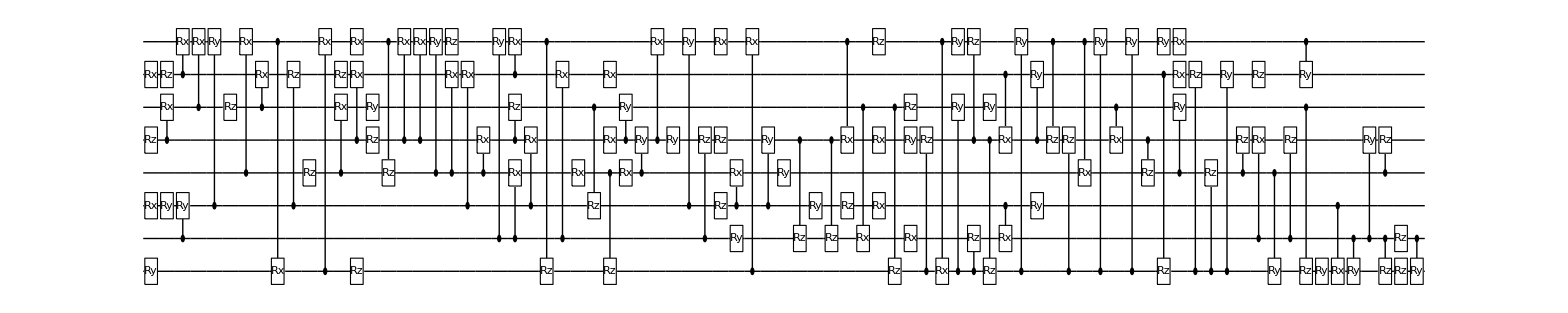

cost=5.31087×10^-6; ngates=117

runtime= 689.47 minutes

cost=5.31087×10^-6 ;dist=0.0111237; globalphase=2.36351

final correlation matrix :(5.94656×10^-6 | 8.45134×10^-6 | 7.0797×10^-6 | 6.90283×10^-6 | 0.0000116893 | 0.0000127062 | 9.46663×10^-6 | 8.39134×10^-6
8.45134×10^-6 | 2.50478×10^-6 | 3.63792×10^-6 | 3.46105×10^-6 | 8.2475×10^-6 | 9.26442×10^-6 | 6.02484×10^-6 | 4.94956×10^-6
7.0797×10^-6 | 3.63792×10^-6 | 1.13314×10^-6 | 2.08941×10^-6 | 6.87587×10^-6 | 7.89279×10^-6 | 4.65321×10^-6 | 3.57792×10^-6
6.90283×10^-6 | 3.46105×10^-6 | 2.08941×10^-6 | 9.56267×10^-7 | 6.69899×10^-6 | 7.71591×10^-6 | 4.47633×10^-6 | 3.40105×10^-6
0.0000116893 | 8.2475×10^-6 | 6.87587×10^-6 | 6.69899×10^-6 | 5.74273×10^-6 | 0.0000125024 | 9.26279×10^-6 | 8.1875×10^-6
0.0000127062 | 9.26442×10^-6 | 7.89279×10^-6 | 7.71591×10^-6 | 0.0000125024 | 6.75964×10^-6 | 0.0000102797 | 9.20442×10^-6
9.46663×10^-6 | 6.02484×10^-6 | 4.65321×10^-6 | 4.47633×10^-6 | 9.26279×10^-6 | 0.0000102797 | 3.52007×10^-6 | 5.96485×10^-6
8.39134×10^-6 | 4.94956×10^-6 | 3.57792×10^-6 | 3.40105×10^-6 | 8.1875×10^-6 | 9.20442×10^-6 | 5.96485×10^-6 | 2.44478×10^-6)

```mathematica
CompileMe[8,unitary8,conf8]
```

#### 10 - QFT

```mathematica
unitary10=CalcCircuitMatrix@Flatten@QFT[10,False];
conf10=DefaultConfig[10,unitary10,30];
```

```mathematica
CompileMe[10,unitary10,conf10]
```